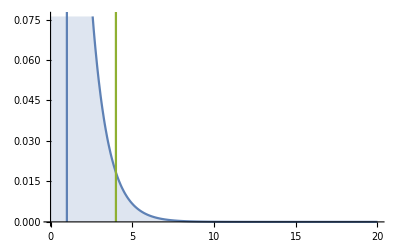

```mathematica
disp=ExponentialDistribution[1];
Show[Plot[PDF[disp,x]//Evaluate,{x,0,20},Filling->Axis], ParametricPlot[{{Mean[disp], y}, {Mean[disp]-3*StandardDeviation[disp], y}, {Mean[disp]+3*StandardDeviation[disp], y}}, {y, 0, 5}]]
```

```mathematica
Exp[-4]//N
```

0.0183156

```mathematica
fx[t_]:=∑_(k=1)^∞ (ⅈ^k Subscript[a, k])/(k!)t^k 
Series[fx[t/(s*Sqrt[n])], {t, 1, 3}]
```

∑_(k=1)^∞ ((ⅈ^k (1/(√n s))^k a_k)/(k!)+(ⅈ^k k (1/(√n s))^k a_k (t-1))/(k!)+(ⅈ^k (-1+k) k (1/(√n s))^k a_k (t-1)^2)/(2 k!)+(ⅈ^k k (2-3 k+k^2) (1/(√n s))^k a_k (t-1)^3)/(6 k!)+O[t-1]^4)

```mathematica
Series[Exp[I*t/(s*Sqrt[n])], {t, 0 ,7}]//FullSimplify//Evaluate
```

1+(ⅈ t)/(√n s)-t^2/(2 (n s^2))-(ⅈ t^3)/(6 n^(3/2) s^3)+t^4/(24 n^2 s^4)+(ⅈ t^5)/(120 n^(5/2) s^5)-t^6/(720 (n^3 s^6))-(ⅈ t^7)/(5040 n^(7/2) s^7)+O[t]^8

```mathematica
Series[Log[1+Subscript[a, 1]/(s*n^(1/2))I*t-Subscript[a, 2]/(2*n*s^2)t^2-Subscript[a, 3]/(6 n^(3/2)s^3)I*t^3+(Subscript[a, 4] t^4)/(24 n^2 s^4)], {t, 0, 5}]
```

(ⅈ a_1 t)/(√n s)+((a_1^2-a_2) t^2)/(2 n s^2)-(ⅈ (2 a_1^3-3 a_1 a_2+a_3) t^3)/(6 n^(3/2) s^3)+((-6 a_1^4+12 a_1^2 a_2-3 a_2^2-4 a_1 a_3+a_4) t^4)/(24 n^2 s^4)+(ⅈ (24 a_1^5-60 a_1^3 a_2+30 a_1 a_2^2+20 a_1^2 a_3-10 a_2 a_3-5 a_1 a_4) t^5)/(120 n^(5/2) s^5)+O[t]^6